```mathematica
f[x_] = (3x + π)/(√(1+ x^2 + √((1+x^2)^3)))
```

(π+3 x)/(√(1+x^2+√((1+x^2)^3)))

```mathematica
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
```

```mathematica
data=Table[{i h,f[i h]},{i,0,n}]//N;
```

```mathematica
TableForm[data]
```

0. | 2.22144
0.6 | 2.87905
1.2 | 2.69633
1.8 | 2.37169
2.4 | 2.09635
3. | 1.88196
3.6 | 1.71455
4.2 | 1.58116
4.8 | 1.47253
5.4 | 1.38227
6. | 1.30598

```mathematica
m=1;
```

```mathematica
ACoeff1=Table[If[i+j!=0,∑_(k=0)^n (data[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.},{33.,138.6}}

```mathematica
B1:=Table[If[i!=0,∑_(k=0)^n (data[[k+1,2]]*(data[[k+1,1]])^i), ∑_(l=0)^n data[[l+1,2]]], {i, 0, m}];B1
```

{21.6033,55.0907}

```mathematica
A1=LinearSolve[ACoeff1,B1]
```

{2.70024,-0.245435}

```mathematica
Q1[x_]=∑_(i=0)^m (A1[[i+1]]*x^i)
```

```mathematica
2.700241262492689-0.24543495326342923 x

graphD=ListPlot[data,PlotStyle->{Darker,PointSize[0.02]}];
```

2.70024-0.245435 x

```mathematica
graphQ1=Plot[Q1[x],{x,a,b},PlotStyle->Orange];
```

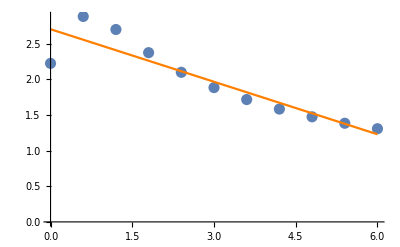

```mathematica
Show[graphD,graphQ1]
```

```mathematica
ACoeff2=Table[If[i+j!=0,∑_(k=0)^n (data[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.,138.6},{33.,138.6,653.4},{138.6,653.4,3283.16}}

```mathematica
m=2;
```

```mathematica
B2:=Table[If[i!=0,∑_(k=0)^n (data[[k+1,2]]*(data[[k+1,1]])^i), ∑_(l=0)^n data[[l+1,2]]], {i, 0, m}];B2
```

{21.6033,55.0907,212.977}

```mathematica
A2=LinearSolve[ACoeff2,B2]
```

{2.65611,-0.196399,-0.00817263}

```mathematica
Q2[x_]=∑_(i=0)^m (A2[[i+1]]*x^i)
```

2.65611-0.196399 x-0.00817263 x^2

```mathematica
graphQ2=Plot[Q2[x],{x,a,b},PlotStyle->Orange];
```

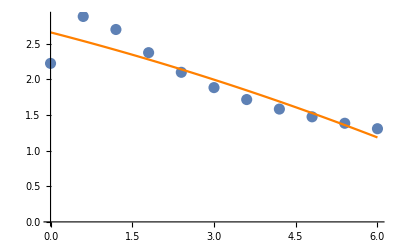

```mathematica
Show[graphD,graphQ2]
```

```mathematica
Q3[x_]=Fit[data,{1,x^1,x^2,x^3},x]
```

2.43256+0.395597 x-0.266912 x^2+0.0287488 x^3

```mathematica
Q4[x_]=Fit[data,{1,x^1,x^2,x^3,x^4},x]
```

2.28919+1.2253 x-0.958332 x^2+0.213128 x^3-0.0153649 x^4

```mathematica
graphQ3=Plot[Q3[x],{x,a,b},PlotStyle->{Green,Thickness[0.01]}];
```

```mathematica
graphQ4=Plot[Q4[x],{x,a,b},PlotStyle->Red];
```

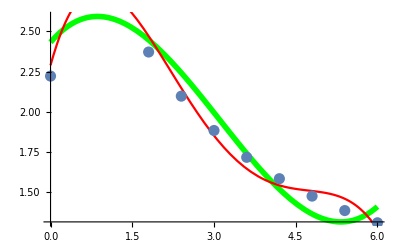

```mathematica
Show[graphQ3,graphQ4,graphD]
```

```mathematica
Print["Q1[x0]=",Q1[x0],", Q2[x0]=",Q2[x0],", Q3[x0]=",Q3[x0],", Q4[x0]=",Q4[x0]]
```

Q1[x0]=2.10344, Q2[x0]=2.13022, Q3[x0]=2.22966, Q4[x0]=2.12936

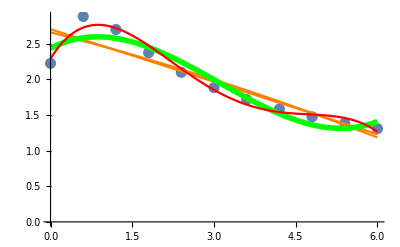

```mathematica
Show[graphD,graphQ1,graphQ2,graphQ3,graphQ4]
```